# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-9);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/results

Real32

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];

Grid[{{
MatrixPlot[He3Norm,FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Norm}",Magnification->2],ImageSize->Medium,PlotRange->Full,PlotLegends->Automatic]
,
MatrixPlot[He3Ham,FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Medium,PlotRange->Full,PlotLegends->Automatic]
}}]
```

-Graphics- | -Graphics-

min/max: {1.07226×10^-15,136.555}

(min/max) discarded elements: 66 {1.07226×10^-15,8.99789×10^-10}

elements < 0: 0

MinMax[Re] = {0.999998,1.}

MinMax[Im] = {0,0}

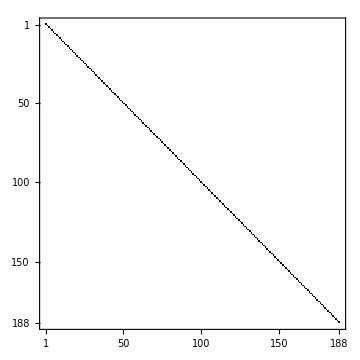

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
He3Norm//MatrixForm;
evn=Eigenvalues[He3Norm];
trafmaa=Transpose[He3Nmhi].He3Norm.He3Nmhi;
trafmaa//MatrixForm;
Grid[{{
MatrixPlot[trafmaa,FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Norm}",Magnification->2],ImageSize->Medium,PlotRange->Full,PlotLegends->Automatic,ColorFunctionScaling->False]
}}]
```

B(^3He) = -8.27189

Dim_full^helion = 254=^!254   ;     Dim_(non - singular)^helion = 188

Norm=1.

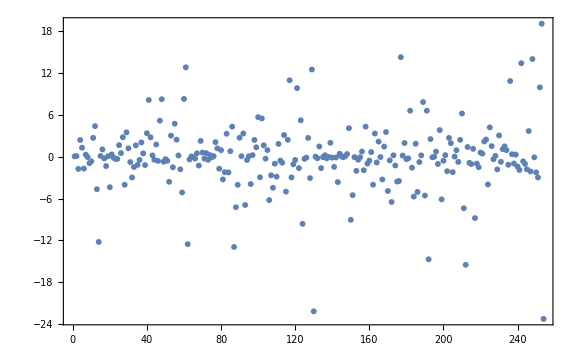
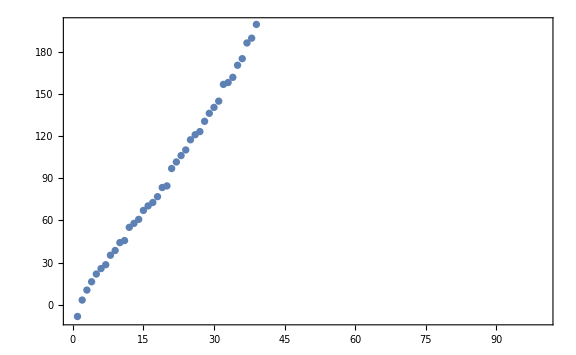
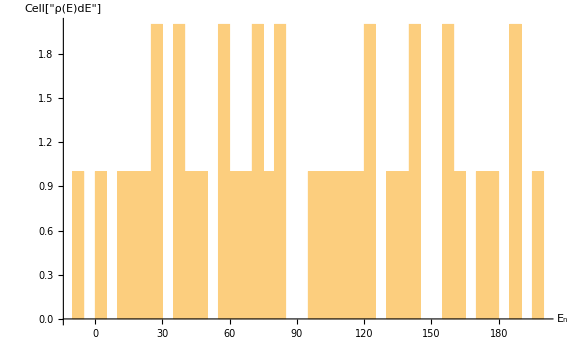
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```